# Problems with SCVT counting

## Initialization

```mathematica
(*Load core package*)
<< CVTUtilites`
```

```mathematica
LaunchKernels[5];
```

## Statistics of appearance of different patterns

### For K-Means clustering

```mathematica
Clear[data];
numTries=100;numSeeds=17;δ=0.01;
data=dataClust[numSeeds,δ,numTries,"Square"];
```

### For random seeded Lloyd process

```mathematica
Clear[data];
numTries=100;numSeeds=17;
tol=10^-5;maxIt=10^4;
data={};
Monitor[
Do[init=RandomPoint[regs["Square"],numSeeds];
AppendTo[data,lloydProc[init,tol,maxIt,"Square",lloydStepFast]]
,{k,numTries}]
,ProgressIndicator[k,{1,numTries}]]
```

### Statistics

You need to prepare data variable from one of the previous cells

```mathematica
dmSquare=DistanceMatrix[data,
DistanceFunction->patternDistSquare,
PerformanceGoal->"Speed"];
```

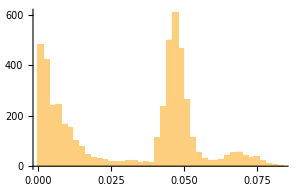

```mathematica
dataDistSquare=Flatten@Table[Drop[dmSquare⟦r⟧,r],{r,numTries}];
histDistSquare = Histogram[dataDistSquare,{0.002}, ImageSize->300]
```

```mathematica
assortment=ReverseSortBy[Tally[Range@numTries,(dmSquare⟦#1,#2⟧≤ 0.02)&],Last];
```

We can see that (for both algorithms) some patterns occur much more often than others. 
And this suggests sadly that for any numTries some patterns may not appear 8(

```mathematica
Row[Row[{tinyRegionPlot[data⟦#⟦1⟧⟧,"Square",70],#⟦2⟧},Frame->True]&/@assortment,"    "]
```

-Graphics-46-Graphics-44-Graphics-2-Graphics-2-Graphics-2-Graphics-1-Graphics-1-Graphics-1-Graphics-1

## Tolerance of iterations

Prepare data for Disk with 7 seeds.

```mathematica
Clear[data];
numTries=200;numSeeds=7;δ=0.01;
data=dataClust[numSeeds,δ,numTries,"Disk"];
```

```mathematica
dataPolar=SortBy[polarRotateC[#,2π],First]&/@ToPolarCoordinates[data];
dataDistDisk={};
dmDisk=Array[0&,{numTries,numTries}];
Monitor[Do[
rotations=polarRotateC[dataPolar⟦i⟧,#]&/@ Range[0,2π,δ];
Do[
dist=Min[polarDistC[dataPolar⟦j⟧,#]&/@rotations];
AppendTo[dataDistDisk,dist];
dmDisk⟦i,j⟧=dmDisk⟦j,i⟧=dist
,{j,i+1,numTries}]
,{i,numTries}],i]
```

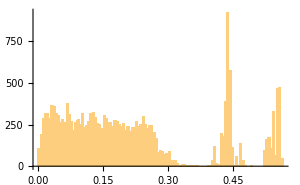

```mathematica
histDistDisk=Histogram[dataDistDisk,{0.005},ImageSize->300]
```

Select distinct (on this stage) types of patterns.
There should be three types here! If not, run dataClust again.

```mathematica
resGatherDiskPolar = dataPolar⟦First/@Gather[Range@numTries,(dmDisk⟦#1,#2⟧<0.2)&]⟧;
resGatherDisk= Map[myFPC,resGatherDiskPolar,{2}];
tinyPlots[ resGatherDisk , "Disk",50,5]
```

-Graphics-

Here are saved examples of all types:

```mathematica
Subscript[ex, 7 dsk1]=;
Subscript[ex, 7dsk2]=;
Subscript[ex, 7dsk3]=;
```

```mathematica
Subscript[tol, 1]=10^-5;Subscript[tol, 2]=10^-6;Subscript[tol, 3]=10^-8;
Subscript[tmpData, 11]=NestWhileList[lloydStepFast[#,"Disk"]&,Subscript[ex, 7dsk2],arrDistCTot[#1,#2]>Subscript[tol, 1]&,2,10^4];
Subscript[tmpData, 12]=NestWhileList[lloydStepFast[#,"Disk"]&,Subscript[ex, 7dsk2],arrDistCTot[#1,#2]>Subscript[tol, 3]&,2,10^5];
Subscript[tmpData, 21]=NestWhileList[lloydStepFast[#,"Disk"]&,Subscript[ex, 7dsk3],arrDistCTot[#1,#2]>Subscript[tol, 1]&,2,10^4];
Subscript[tmpData, 22]=NestWhileList[lloydStepFast[#,"Disk"]&,Subscript[ex, 7dsk3],arrDistCTot[#1,#2]>Subscript[tol, 2]&,2,10^5];
```

We can see that accuracy 10^-5 for example ex_(7dsk3) is achieved in just three steps, and the pattern seems to stabilize. 
But it is enough to make the accuracy equal to 10^-6, and in 30-40 steps the pattern is reduced to another type.

```mathematica
Manipulate[tinyPlot[Subscript[tmpData, 21]⟦i⟧ , "Disk",100],{i,1,Length@Subscript[tmpData, 21],1},SaveDefinitions->True]
```

```mathematica
Manipulate[tinyPlot[Subscript[tmpData, 22]⟦i⟧ , "Disk",100],{i,1,Length@Subscript[tmpData, 22],1},SaveDefinitions->True]
```

Pattern ex_(7 dsk1) stay stable up to 10^-8 accuracy

```mathematica
Manipulate[tinyPlot[Subscript[tmpData, 12]⟦i⟧ , "Disk",100],{i,1,Length@Subscript[tmpData, 12],1},SaveDefinitions->True]
```